# Confluence in Multiway Cellular Automata

## Singleway and Multiway Cellular Automata

In the simplest case of a normal, singleway Cellular Automaton (CA), rows of black and white cells are built up by applying a rule to each cell and its neighbors to find the color of each cell in the next row. This case corresponds to a one-dimensional, two-color, nearest-neighbor CA called an elementary CA. A multiway CA is a modification of this system where only one replacement from the rule is applied at one position per step. This is the behavior of elementary rule 110 as a singleway and multiway system:

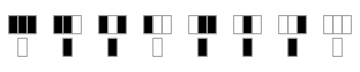
-Graphics--Graphics-
-Graphics-Left: Singleway behavior of rule 110 from a random initial condition
Right: Multiway state transitions of rule 110 from all initial conditions of five cells
Bottom: Plot of cell replacements corresponding to rule 110

```mathematica
multi=ResourceFunction["MultiwaySystem"];
render="StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->30],#1,#3]&);
statesGraph=multi[CellularAutomaton[110],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->{300,300}];
Labeled[Column[{Row[{
ArrayPlot[CellularAutomaton[110,RandomInteger[1,200],200],ImageSize->{300,300}],statesGraph
}],
RulePlot[CellularAutomaton@110,ImageSize->Medium]},Alignment->Center],
Text["Left: Singleway behavior of rule 110 from a random initial condition
Right: Multiway state transitions of rule 110 from all initial conditions of five cells
Bottom: Plot of cell replacements corresponding to rule 110"]]
```

Multiway CA’s can also be visualized by constructing singleway CA plots from different possible paths through the multiway system. This shows some of the possible paths through the states graph above starting from the single black cell initial condition:

```mathematica
getAllPathsFromState[graph_,start_,length_]:=
	Flatten[FindPath[graph,start,#,length,All]&/@Rest[VertexOutComponent[graph,start]],1]
getAllPathsToState[graph_,finish_,length_]:=
	Flatten[FindPath[graph,#,finish,length,All]&/@Rest[VertexInComponent[graph,finish]],1]
overlayPaths[paths_]:=ArrayPlot[N@Total[paths]/Length[paths],ImageSize->Medium]
cellStateProbabilities[graph_,init_,length_]:=With[{allPaths=getAllPathsFromState[graph,init,length]},
	Table[N@Mean[#[[i]]&/@Select[allPaths,Length[#]≥i&]],{i,length}]]
graph=multi[CellularAutomaton[110],CenterArray[1,10],10,"StatesGraph",render,ImageSize->Medium];
paths=RandomSample[getAllPathsFromState[graph,CenterArray[1,10],{9}],10];
Row[ArrayPlot[#,ImageSize->{80,96}]&/@paths]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

This can also be viewed by overlaying these graphs to see the chance of cells being different colors at different steps, or by stacking the paths from different  branches:

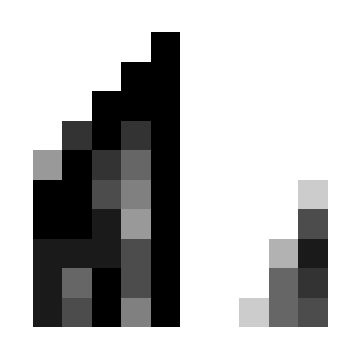
-Graphics--Graphics3D-

```mathematica
Row[{overlayPaths[paths],ArrayPlot3D[paths,OpacityFunction->.7,ImageSize->Medium]}]
```

## Testing for Confluence

This project aims to study confluence in multiway cellular automata. A graph is confluent where for every node, every branch from the node can always merge back into some other state. I also define total confluence as a graph where every node can always reach every other node, regardless of branching. For any multiway state graph, confluence can be shown by checking that for every disjointed piece of the graph, there is some state that every other state eventually connects to. This is tested for each island in the graph because only branches from the same state must merge. Total confluence can be tested by checking that every node is connected to every other node in its island from both directions at some distance. These methods should be applicable for any type of single-edge multiway system.

```mathematica
confluentQ[graph_] := AllTrue[WeaklyConnectedGraphComponents[graph],
	Function[cc, AnyTrue[VertexList[cc], ContainsExactly[VertexInComponent[cc, #], VertexList[cc]] &]]]
totalConfluentQ[graph_] := CompleteGraphQ[TransitiveClosureGraph[graph]]
```

This is the states graph for rule 110 from every initial condition. This graph is confluent, as all the outside states from the main subgraph can always reach one of the states in the central loop. It is not totally confluent, as the outside states cannot be reached from the inside ones, and the all white state cannot reach or be reached by any other state:

```mathematica
Row[{multiwayGraph=ResourceFunction["MultiwaySystem"][CellularAutomaton[110],Tuples[{0,1},5],1,"StatesGraph","StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->25],#1,#3]&),ImageSize->Medium],Column[{Text["Confluent: "<>ToString@confluentQ[multiwayGraph]],Text["Total Confluent: "<>ToString@totalConfluentQ[multiwayGraph]]}]},"\t"]
```

-Graphics-Confluent: True
Total Confluent: False

I call the states which the system can always reach confluent end states. In this case, the confluent end states are the central connected portion of the graph, as well as the all white island state:

```mathematica
getConfluentEndStates[graph_]:=Function[cc,Select[VertexList[cc],
	ContainsExactly[VertexInComponent[cc,#],VertexList[cc]]&]]/@WeaklyConnectedGraphComponents[graph]
```

```mathematica
Row[ArrayPlot[{#},ImageSize->50]&/@Flatten[getConfluentEndStates[multiwayGraph],1]," "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Confluence by Rule Behavior

Cellular automata can be divided into four classes based on their behavior. Class 1 automata quickly become uniform, class 2 repetitive, class 3 appear mostly random, and class 4 have localized structures interacting in complex ways. This chart shows the singleway behavior of three automata from each class, along with the states graph and confluence of their corresponding multiway systems:

```mathematica
caByClass=Association[1->{4,8,255},2->{9,15,154},3->{30,89,149},4->{110,124,137}];
Column[Table[Grid[Join[{{"","",Text["Class "<>ToString[i]],"",""}},{Text/@{"Rule","Plot","States","Confluent","Total Conf.","Conf. Ends"}},({#1,ArrayPlot[CellularAutomaton[#1,RandomInteger[1,100],100]],g=multi[CellularAutomaton[#1],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->Medium],confluentQ[g],totalConfluentQ[g],Length[Flatten[getConfluentEndStates[g],1]]}&)/@caByClass[i]],Frame->{False,All}],{i,4}]]
```

-Graphics-

It’s impossible to draw concrete conclusions from this small sample size, especially because there is only one distinct class 4 elementary CA, but I will generalize some observations nonetheless. Qualitatively, there does not seem to be a correlation between rule class and confluence, but the structure of the state graphs are generally similar for rules with similar singleway behavior. Class 1 automata must maintain their states after a certain point by definition. Class 2 automata seem to produce multiway state graphs with a more regular structure, though the complex repeated pattern of singleway rule 154 does not lend itself to a straightforward states graph representation. Class 3 automata show very complicated branching paths that aren’t easy to analyze, much like their singleway counterparts. All of the class 4 elementary automata are simple transformations of rule 110, but seem to produce state graphs with slightly different structures. They all have a mostly regular form with some complications, which could be related to their singleway behavior of a regular background with pockets of complex interactions.

## More Multiway CA Behaviors

I mostly studied small cell tape widths, as any representation of any multiway CA grew in size and complexity much faster than for singleway systems. I found that the behavior of many rules changed for different numbers of cells, including whether or not the system was confluent. This shows the states graph structure for one rule from each class from all initial conditions of different cell tape widths:

```mathematica
Labeled[Grid[Table[Column[{g=multi[CellularAutomaton[rule],Tuples[{0,1},cells],1,"StatesGraphStructure",ImageSize->{150,150}],confluentQ@g}],{rule,{4,9,30,110}},{cells,5}],Frame->All],Text["States graph structure for rules 4, 9, 30, and 110 (down) with 1-5 cells (right) and their confluence"]]
```

-Graphics-

I found that most multiway elementary CA rules are confluent, but that confluence depends on the width of the cell rows as well as the rule . Only a few multiway CA' s were totally confluent . Confluence of one rule can fluctuate based on cell tape width in a variety of ways.

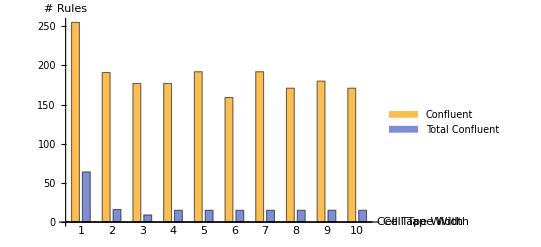

```mathematica
getAllElementaryGraphs[maxCells_]:=
	Table[multi[CellularAutomaton[i],Tuples[{0,1},j],1,"StatesGraphStructure"],{i,255},{j,maxCells}];
getConfluenceByCells[allGraphs_]:=Transpose@Map[confluentQ,allGraphs,{2}]
getTotalConfluenceByCells[allGraphs_]:=Transpose@Map[totalConfluentQ,allGraphs,{2}]
getConfluenceCountsByCells[confluenceByCells_]:=
	Table[Count[confluenceByCells[[i]],True],{i,Length@confluenceByCells}]
getBothConfluenceCounts[allGraphs_]:=With[{
	confluenceCountsByCells=getConfluenceCountsByCells[getConfluenceByCells[allGraphs]],
	totalConfluenceCountsByCells=getConfluenceCountsByCells[getTotalConfluenceByCells[allGraphs]]},
	Table[{confluenceCountsByCells[[i]],totalConfluenceCountsByCells[[i]]},{i,Length@confluenceCountsByCells}]]
BarChart[getBothConfluenceCounts[getAllElementaryGraphs[10]],ChartLabels->{Placed[Range[10],Below],None},AxesLabel->{Text["Cell Tape Width"],"# Rules"},ChartLegends->{"Confluent","Total Confluent"}]
```

So far I’ve only shown the states graph for multiway cellular automata. A complimentary view is the causal graph, which shows the interactions between different rule applications directly. This shows the structure of the states graphs and causal graphs for multiway rule 110 for cell tape widths up to five, along with their confluence and the CausalInvariantQ property from the MultiwaySystem function:

```mathematica
Grid[Prepend[Table[{i,g=multi[CellularAutomaton@30,Tuples[{0,1},i],1,"StatesGraphStructure",ImageSize->{250,250}],SimpleGraph@multi[CellularAutomaton@30,Tuples[{0,1},i],3,"CausalGraphStructure",ImageSize->{250,250}],
Text@confluentQ@g,Text@multi[CellularAutomaton@30,Tuples[{0,1},i],3,"CausalInvariantQ"]
},{i,5}],Text/@{"Cells","States Graph","Causal Graph","Confluent","CausalInvariantQ"}],Frame->All]
```

-Graphics-

Max Piskunov observed that the CausalInvariantQ property actually measured confluence, but that isn’t consistent with these examples. It does not seem to measure causal invariance here either, as the  It’s possible that the CausalInvariantQ property does not correctly identify either confluence or causal invariance for non-terminating systems, which may be a problem with the function or with the definition of these terms for non-terminating systems such as these.
	In general, these multiway cellular automata start to show some forms of complex behavior with around four cells. I’ve also found some complexity with using single-neighbor rules (instead of looking at neighbors on both sides). This shows the states graph and causal graph structure for the first eight of these single-neighbor rules with five cells after three steps:

```mathematica
singleNeighborRule;singleNeighborRule[rule_]:=MapThread[#1->{#2,Last@#1}&,{Tuples[{0,1},2],IntegerDigits[rule,2,4]}]
showRule;showRule[singleNeighborRule_,size_]:=Grid[Transpose[{ArrayPlot[{Keys@#},ImageSize->{size*2,size}],ArrayPlot[{{First@Values@#}},ImageSize->{size,size}]}&/@singleNeighborRule]]
Grid[Table[{showRule[singleNeighborRule[rule],10],g=multi[singleNeighborRule[rule],Tuples[{0,1},5],1,"StatesGraph","StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->{30,10}],#1,#3]&),ImageSize->Medium],
SimpleGraph@multi[singleNeighborRule[rule],Tuples[{0,1},5],3,"CausalGraphStructure"],confluentQ@g},{rule,0,7,1}],Frame->All]
```

-Graphics-

## Future Work

I would like to study the relationship between confluence of a multiway CA and the behavior of its singleway counterpart in more detail. This would probably require an automatic classification system of the behavior of singleway cellular automata. It’s also difficult to find concrete results as there is only one truly distinct elementary CA with class 4 behavior. So, I would also like to study different classes of CA rules.
	The next step is to study the relationship between causal variance and confluence. Causal variance is a property similar to confluence but for the causal graph of the system, which shows how different updating events affect each other. I did not find an immediate correlation between these properties, but the CausalInvariantQ property of the MultiwaySystem resource function does not seem to work properly in all cases. So, I need to figure out the issues and fix them before continuing in this direction.
	An important idea that is not yet well understood is universality in multiway systems. Simple systems including singleway elementary cellular automata have been shown to be universal, meaning they can emulate any other system. However, it is not clear that universality can be defined in the same way for multiway systems, or if singleway systems can emulate all multiway systems. I believe universality in multiway systems could be defined based on relations between the causal graphs of different systems,

## Acknowledgements

I would like to thank Christopher Wolfram for being an excellent mentor and guiding me through many aspects of this project from understanding to code and for helping make the summer school a very enjoyable experience. I’d also like to thank Stephen Wolfram for providing the project idea and for pushing me to understand more about the ways multiway systems can behave. Thanks to Jonathan Gorard for his work on creating the extremely extensive MultiwaySystem repository function which provided the foundation for my project, and for helping me understand how to use it properly. Additionally, thanks to Max Piskunov for his work on understanding the relationship between confluence and causal invariance, contributing to the MultiwaySystem function, and understanding how the function measures causal invariance. Finally, thanks to all the administrators at the Wolfram Summer School, including Erin Cherry, Danielle Mayer, and Mads Bahrami, for making this experience possible.